# Modelo versión 3

## Pruebas 30/07

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

Todas las redes:

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/","network-100-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,6,1}];
```

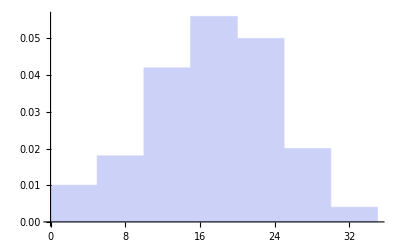
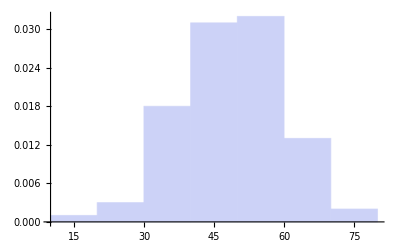
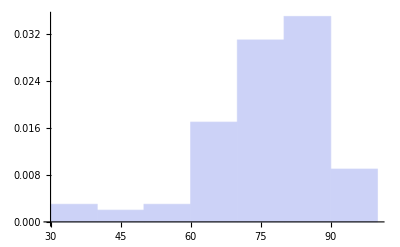
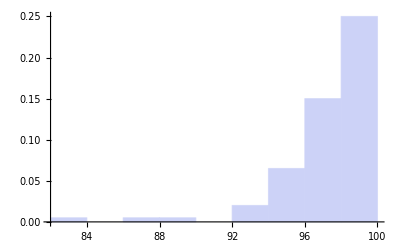
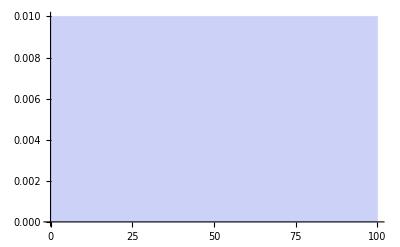
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,6,1}]
```

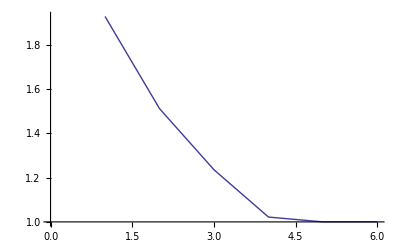

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3];
aplM3=Map[MeanGraphDistance,networksM3];
ListPlot[aplM3,Joined->True]
```

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/","t10000network-1000-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,6,1}];
```

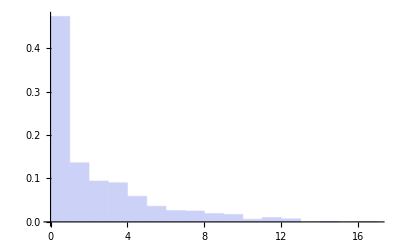
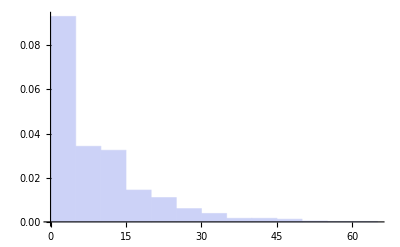
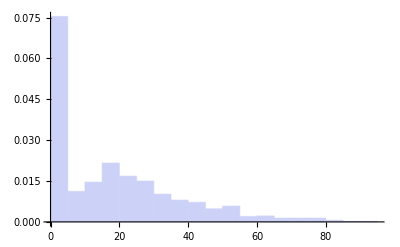
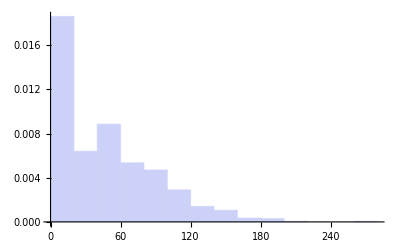
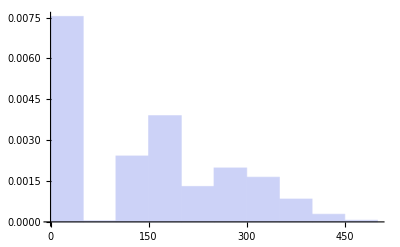
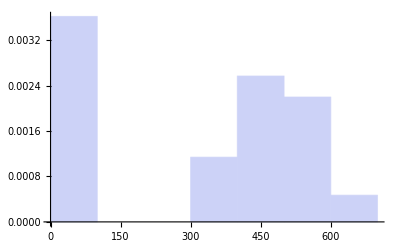

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,6,1}]
```

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/p10000/","network-10000-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,2,1}];
```

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,2,1}]
```

# Modelo versión 3

## Pruebas 31/07

Lim-capacity: [1-50] --> 5

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000/","network-100-",IntegerString[i],".graphml"]],{i,1,50,5}];
```

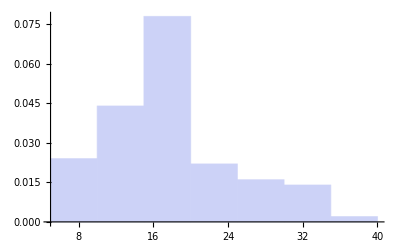
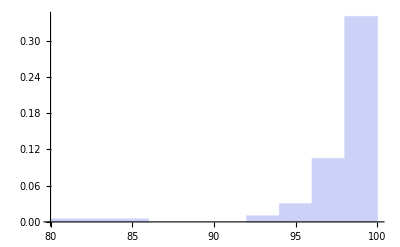
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[VertexDegree[networks100Fixed[[i]]],Automatic,"PDF"],{i,1,Length[networks100Fixed],1}]
```

```mathematica
network1000Fixed1=Import[StringJoin["graphs/model-v3/fixed-t1000/","network-1000-1.graphml"]];
```

```mathematica
network1000Fixed10=Import[StringJoin["graphs/model-v3/fixed-t1000/","network-1000-46.graphml"]];
```

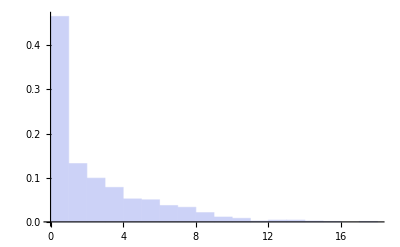
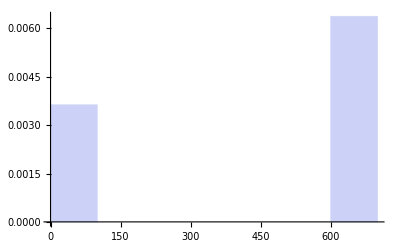

```mathematica
{Histogram[VertexDegree[network1000Fixed1],Automatic,"PDF"],Histogram[VertexDegree[network1000Fixed10],Automatic,"PDF"]}
```

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000/","network-100-",IntegerString[i],".graphml"]],{i,1,50,5}];
```

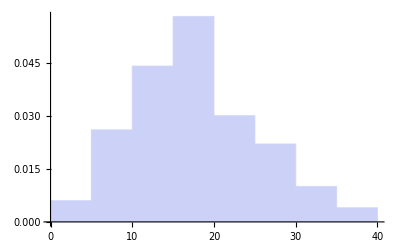
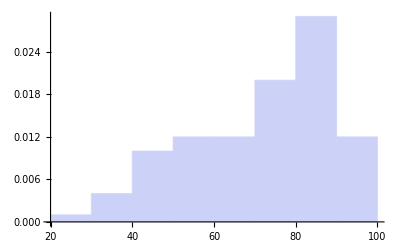
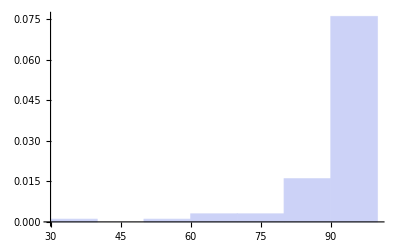
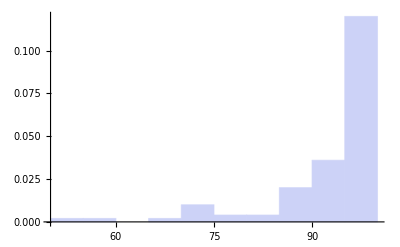
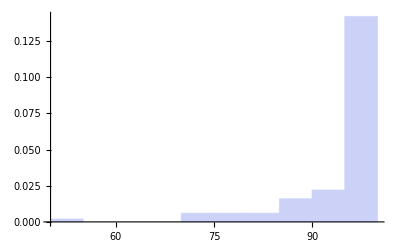
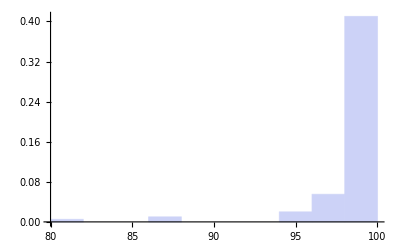
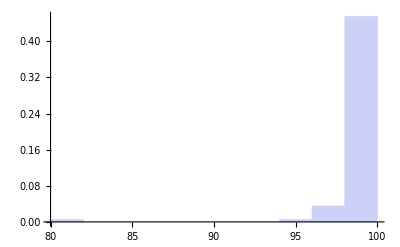
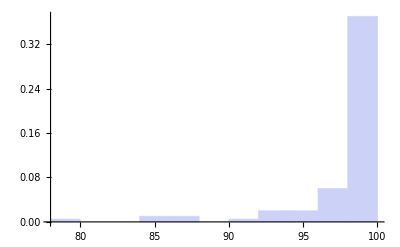

```mathematica
Table[Histogram[VertexDegree[networks100Uniform[[i]]],Automatic,"PDF"],{i,1,Length[networks100Uniform],1}]
```

```mathematica
network1000Uniform1=Import[StringJoin["graphs/model-v3/uniform-t1000/","network-1000-1.graphml"]];
```

```mathematica
network1000Uniform10=Import[StringJoin["graphs/model-v3/uniform-t1000/","network-1000-46.graphml"]];
```

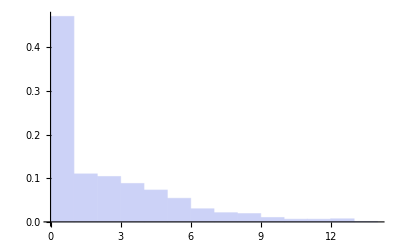
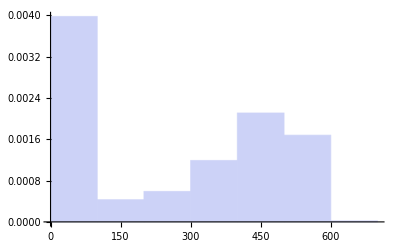

```mathematica
{Histogram[VertexDegree[network1000Uniform1],Automatic,"PDF"],Histogram[VertexDegree[network1000Uniform10],Automatic,"PDF"]}
```

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000/","network-100-",IntegerString[i],".graphml"]],{i,1,50,5}];
```

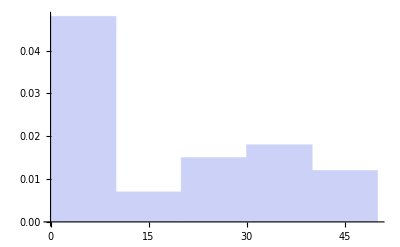
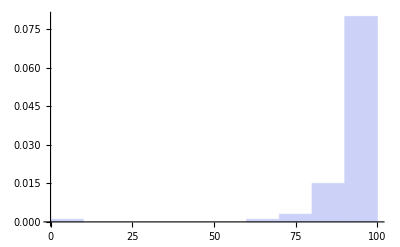
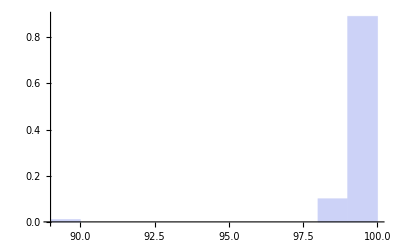
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[VertexDegree[networks100Normal[[i]]],Automatic,"PDF"],{i,1,Length[networks100Normal],1}]
```

```mathematica
networks1000Normal1=Import[StringJoin["graphs/model-v3/normal-t1000/","network-1000-1.graphml"]];
```

```mathematica
networks1000Normal10=Import[StringJoin["graphs/model-v3/normal-t1000/","network-1000-46.graphml"]];
```

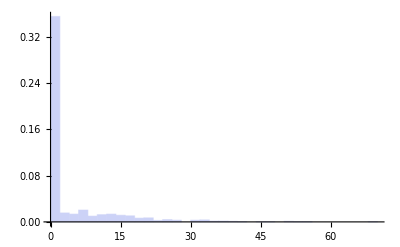
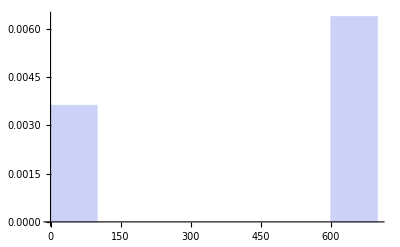

```mathematica
{Histogram[VertexDegree[networks1000Normal1],Automatic,"PDF"],Histogram[VertexDegree[networks1000Normal10],Automatic,"PDF"]}
```

# Modelo versión 3

## Pruebas 31/07

Lim-capacity: [1-10] --> 1

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

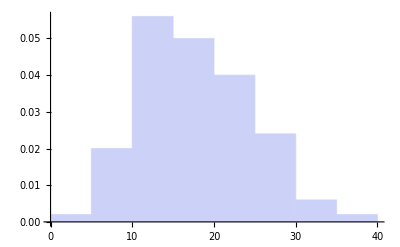
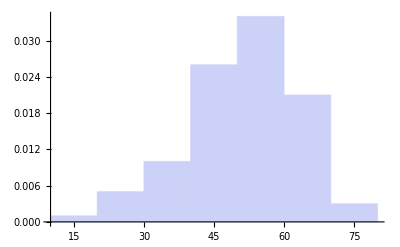
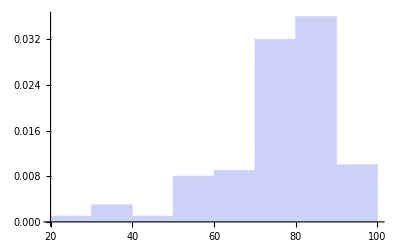
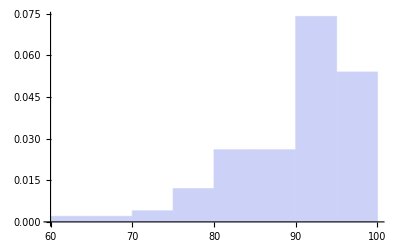
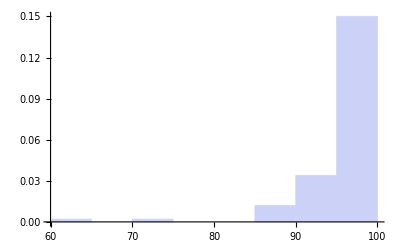
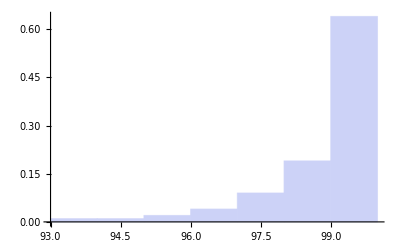
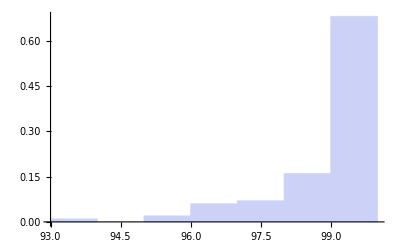
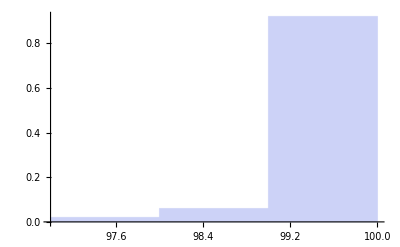

```mathematica
Table[Histogram[VertexDegree[networks100Fixed[[i]]],Automatic,"PDF"],{i,1,Length[networks100Fixed],1}]
```

```mathematica
networks1000Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

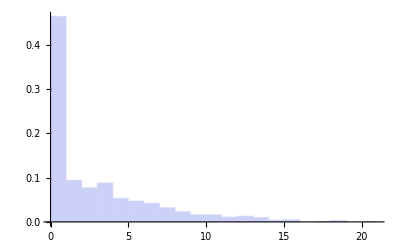
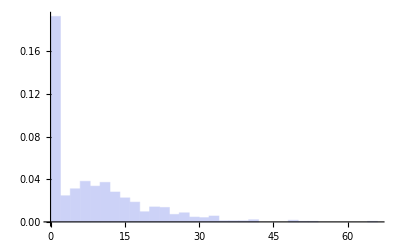
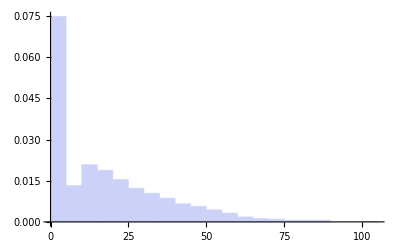
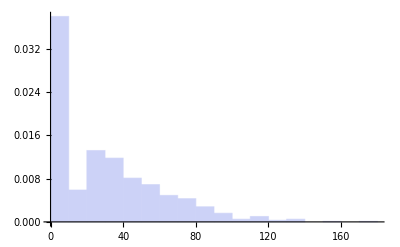
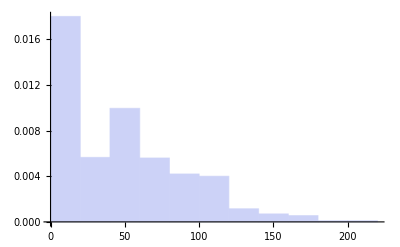
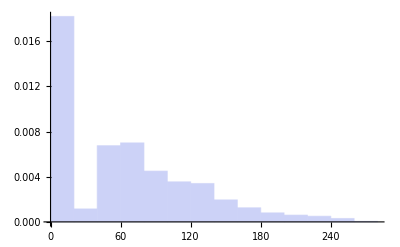
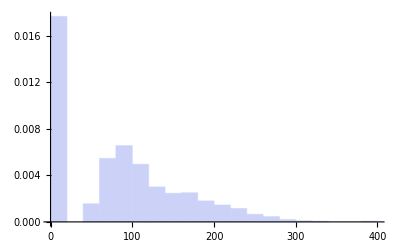
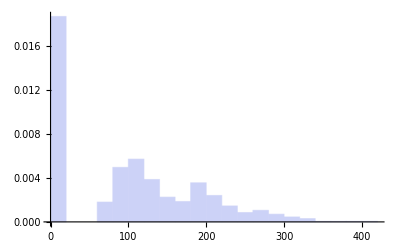

```mathematica
Table[Histogram[VertexDegree[networks1000Fixed[[i]]],Automatic,"PDF"],{i,1,Length[networks1000Fixed],1}]
```

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

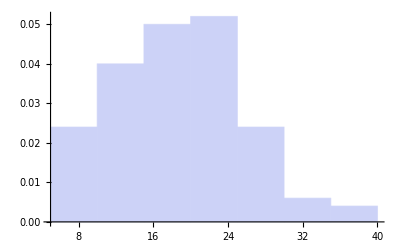
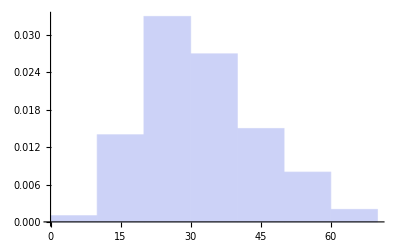
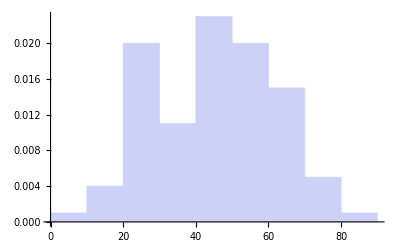
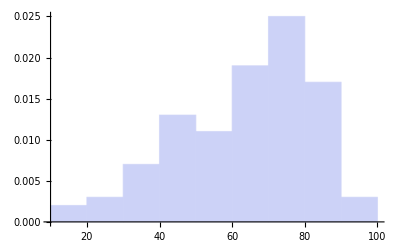
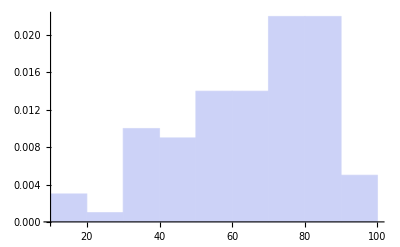
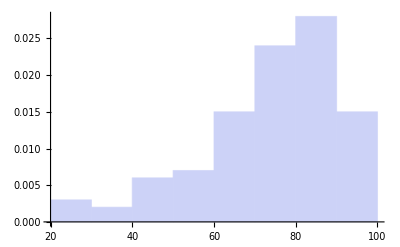
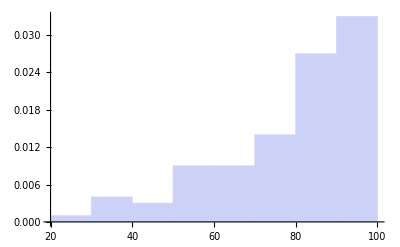
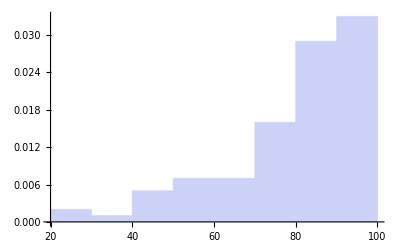

```mathematica
Table[Histogram[VertexDegree[networks100Uniform[[i]]],Automatic,"PDF"],{i,1,Length[networks100Uniform],1}]
```

```mathematica
networks1000Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

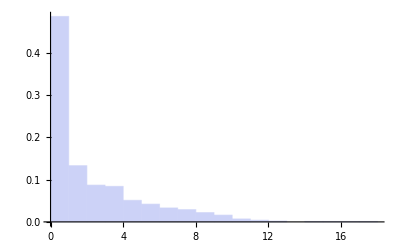
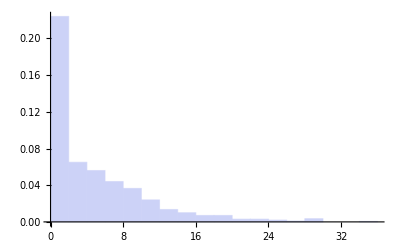
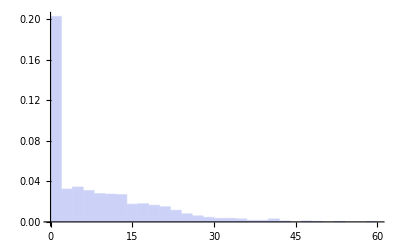
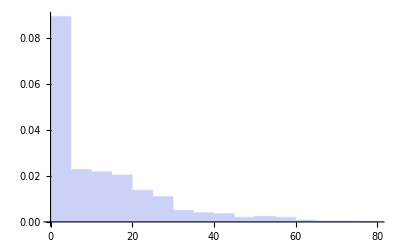
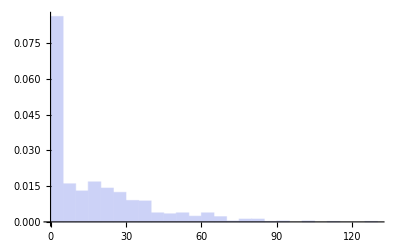
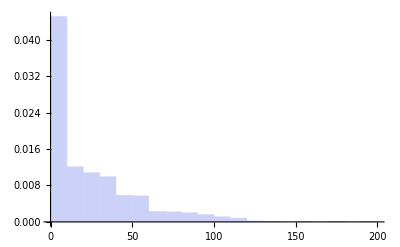
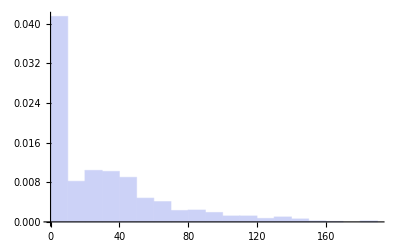
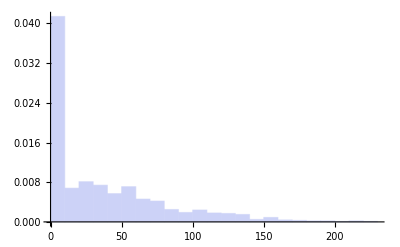

```mathematica
Table[Histogram[VertexDegree[networks1000Uniform[[i]]],Automatic,"PDF"],{i,1,Length[networks1000Uniform],1}]
```

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

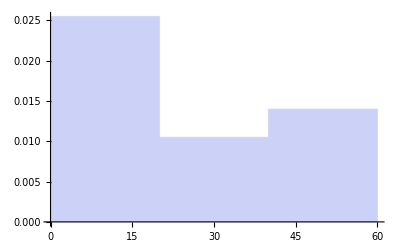
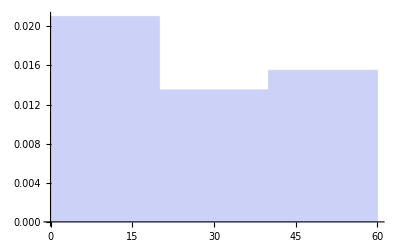
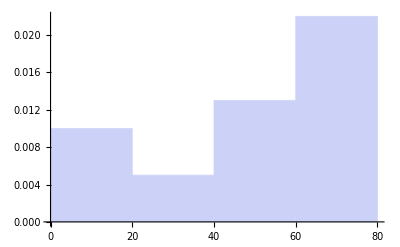
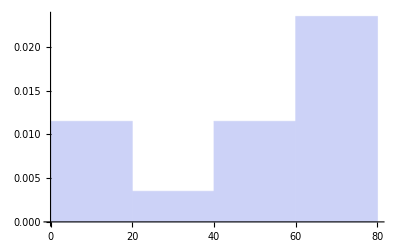
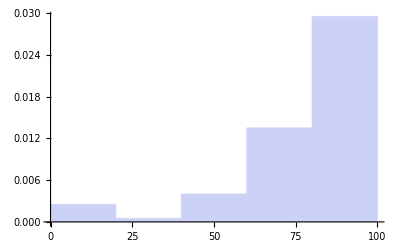
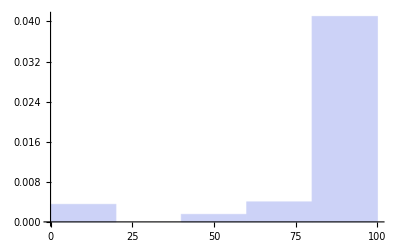
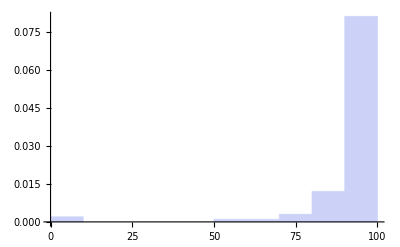
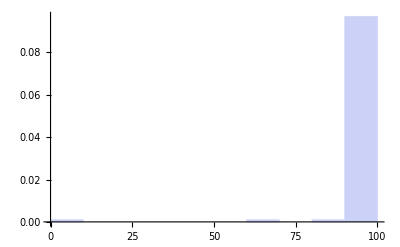

```mathematica
Table[Histogram[VertexDegree[networks100Normal[[i]]],Automatic,"PDF"],{i,1,Length[networks100Normal],1}]
```

```mathematica
networks1000Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

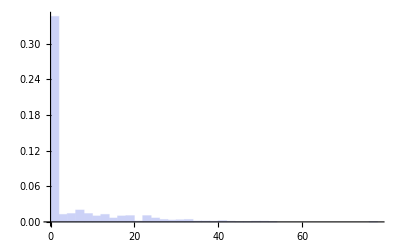
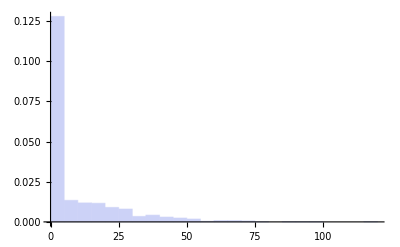
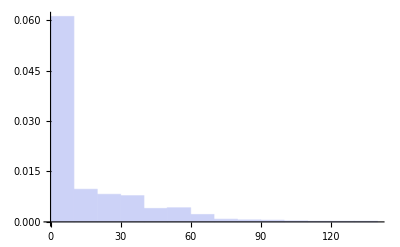
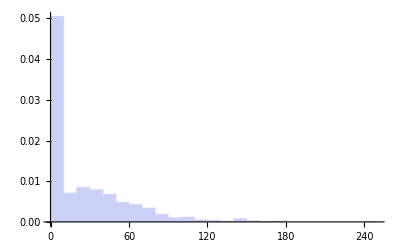
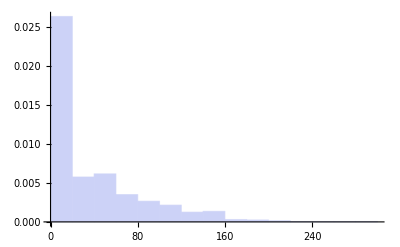
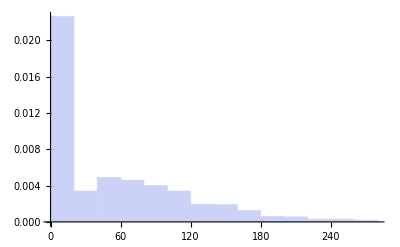
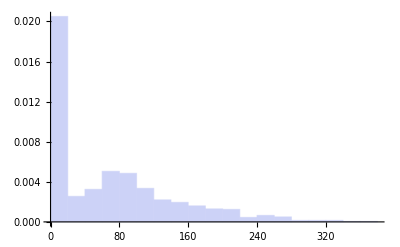
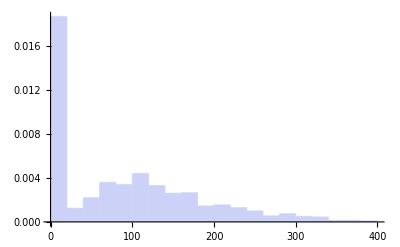

```mathematica
Table[Histogram[VertexDegree[networks1000Normal[[i]]],Automatic,"PDF"],{i,1,Length[networks1000Normal],1}]
```

# Modelo versión 3

## Pruebas 02/08

Lim-capacity: [1-10] --> 1
10.000 unidades de tiempo

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Fixed[[i]]],Automatic,"PDF"],{i,1,Length[networks100Fixed],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Uniform[[i]]],Automatic,"PDF"],{i,1,Length[networks100Uniform],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normalt10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Normal[[i]]],Automatic,"PDF"],{i,1,Length[networks100Normal],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Lim-capacity: [1-10] --> 1
100.000 unidades de tiempo

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Fixed[[i]]],Automatic,"PDF"],{i,1,Length[networks100Fixed],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Uniform[[i]]],Automatic,"PDF"],{i,1,Length[networks100Uniform],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normalt100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
Table[Histogram[VertexDegree[networks100Normal[[i]]],Automatic,"PDF"],{i,1,Length[networks100Normal],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}